## Simulated scattering data from spherical bubbles in water with log-normal-distributed radii

Parameters

```mathematica
Rmin = 0.001; (* minimum observable radius, nondim by Rmax *)
Rmax = 1; (* maximum observable radius, nondim by Rmax *)
ρs = 1; (* density of solvent, nondim by ρs *)
ρv = 0.1; (* density of vapor bubble, nondim by ρs *)
Δρ = ρv - ρs; (* density difference between vapor and solvent [kg/m^3] *)
logμR =-1.242; (* log of arbitrary mean bubble radius, nondim by Rmax *)
logσ= 1.0481; (* standard deviation of log of bubble radius, nondim by Rmax *)
A = 1; (* arbitrary amplitude for scaling the number of bubbles *)
```

Relevant functions

```mathematica
V[R_]:= 4π/3 R^3; (* volume V of a sphere of radius R *)
Num[R_,logμ_,logσ_,A_]:=A/(R Sqrt[2 π logσ^2] )Exp[-(Log[R]-logμ)^2/(2logσ^2)];
Amp[s_,R_]:= 4π R^3/3 (Sin[s R]-s R Cos[s R])/(s R)^3; (* scattering amplitude of a sphere, from Svergun and Koch 2003 *)
I0[s_,R_]:= (Amp[s,R])^2;
i0[s_,R_]:=I0[s,R]/Limit[I0[a,R],a->0]; (* normalized scattering intensity of one spherical particle *)
```

Compute the function for the scattering pattern produced by log-normal-distributed spherical bubbles

```mathematica
sVec=Table[10^(i/100),{i,0,300}];
```

```mathematica
scatteringData=Table[{sVec[[i]],(Δρ)^2NIntegrate[Num[R,logμR,logσ,A] (V[R])^2 i0[sVec[[i]],R],{R,Rmin, Rmax}]},{i,1,Length[sVec]}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["large_variance.pdf",ListLogLogPlot[scatteringData,Axes->True,AxesLabel->{"s [1/Rmax]","intensity [a.u.]"},PlotLabel->"Log-normal-distr. bubbles, μ = "<>ToString[logμR]<>", σ = "<>ToString[logσ],BaseStyle->{FontSize->12}]]
```

large_variance.pdf

## Save Plots of Scattering Intensity for Different mean and standard deviation

### Change mean (logμ)

```mathematica
SetDirectory[NotebookDirectory[]];
μList = {Log[0.005],Log[0.05],Log[0.5]};
σList={0.5,1,2};
sVec=Table[N[10^(i/100)],{i,0,400}];
```

Save data only

```mathematica
For[i=1,i≤Length[μList],i++, For[j=1,j≤Length[σList],j++,μ=μList[[i]];σ=σList[[j]];μLabel = ToString[Round[1000*Exp[μ]]];σLabel=ToString[Round[1000*σ]];scatteringData=Table[{sVec[[i]],(Δρ)^2NIntegrate[Num[R,μ,σ,A] (V[R])^2 i0[sVec[[i]],R],{R,Rmin, Rmax}]},{i,1,Length[sVec]}];
dataName = "saxs_data_mu_"<>μLabel<>"_sigma_"<>σLabel<>".csv";
Export[dataName,scatteringData];]]
```

```mathematica
For[i=1,i≤Length[μList],i++, For[j=1,j≤Length[σList],j++,μ=μList[[i]];σ=σList[[j]];μLabel = ToString[Round[1000*Exp[μ]]];σLabel=ToString[Round[1000*σ]];(*scatteringData=Table[{sVec[[i]],(Δρ)^2NIntegrate[Num[R,μ,σ,A] (V[R])^2 i0[sVec[[i]],R],{R,Rmin, Rmax}]},{i,1,Length[sVec]}];
saveNameSAXS="saxs_data_mu_"<>μLabel<>"_sigma_"<>σLabel<>".pdf";
Export[saveNameSAXS,ListLogLogPlot[scatteringData,Axes->True,AxesLabel->{"s [1/Rmax]","intensity [a.u.]"},PlotLabel->"Log-normal-distr. bubbles, μ = "<>ToString[μ]<>", σ = "<>ToString[σ],BaseStyle->{FontSize->12}]]];*)
rVec = Table[10^(i/100),{i,-600,300}];numberData = Table[{rVec[[i]],Num[rVec[[i]],μ,σ,A]},{i,1,Length[rVec]}];
dataName = "SAXS_data_mu_"<>μLabel<>"_sigma_"<>σLabel<>".csv";
Export[dataName,numberData];
saveNamePDF = "PDF_mu_"<>μLabel<>"_sigma_"<>σLabel<>".pdf";Export[saveNamePDF,ListLogLogPlot[numberData,Axes->True,AxesLabel->{"r [Rmax]","Prob. density"},PlotLabel->"Log-normal-distr. bubbles, μ = "<>ToString[μ]<>", σ = "<>ToString[σ],BaseStyle->{FontSize->12}]]];]
```

$Aborted

Number distribution

```mathematica
rVec = Table[10^(i/100),{i,-600,300}];
```

```mathematica
numberData = Table[{rVec[[i]],Num[rVec[[i]],logμR,logσ,A]},{i,1,Length[rVec]}];
```

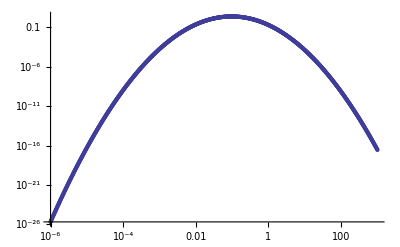

```mathematica
ListLogLogPlot[numberData]
```

Single sphere as benchmark

```mathematica
sVec = Table[10^(i/400),{i,-50,500}];
```

```mathematica
singleSphere = Table[{sVec[[i]],I0[sVec[[i]],Rmax]},{i,1,Length[sVec]}];
```

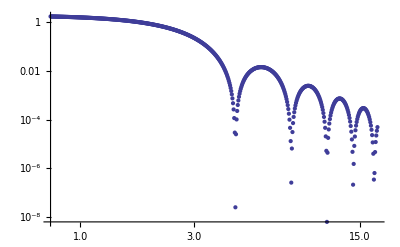

```mathematica
ListLogLogPlot[singleSphere]
```

#### Sample plot of a log-normal distribution

```mathematica
μ=Log[100];
σ=1;
A = 1;
Rmin = 1;
Rmax = 1350;
```

```mathematica
dataTheory = Table[{Exp[i/100],Num[Exp[i/100],μ,σ,A]},{i,0,700}];
dataExp = Table[{Exp[i/10],Num[Exp[i/10],μ,σ,A]*(1+RandomVariate[NormalDistribution[0,0.5]])},{i,0,70}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
μLabel = ToString[Round[Exp[μ]]];σLabel=ToString[Round[σ]];
saveNamePDF = "PDF_log_normal_theory_exp_mu_"<>μLabel<>"_sigma_"<>σLabel<>".pdf";Export[saveNamePDF,ListLogLogPlot[{dataTheory,dataExp},Axes->True,AxesLabel->{"r [nm]","Prob. density"},PlotLabel->"Log-normal-distr. bubbles, μ = "<>ToString[μ]<>", σ = "<>ToString[σ],BaseStyle->{FontSize->12},PlotLegend->{"theory","experiment"}]];
```

ListLogLogPlot::optx: Unknown option PlotLegend → {"theory", "experiment"} in ListLogLogPlot[{{{1, ⅇ^-1/2\ Power[« 2 »]/√2\ π}, {ⅇ^1/100, ⅇ^-1/100 + Times[« 2 »]/√2\ π}, {ⅇ^1/50, ⅇ^-1/50 + Times[« 2 »]/√2\ π}, {ⅇ^3/100, ⅇ^-3/100 + Times[« 2 »]/√2\ π}, « 44 », {ⅇ^12/25, ⅇ^-12/25 + Times[« 2 »]/√2\ π}, {ⅇ^49/100, ⅇ^-49/100 + Times[« 2 »]/√2\ π}, « 651 »}, {{1, 5.87586×10^-6}, {ⅇ^1/10, 0.000020597}, « 48 », « 21 »}}, « 4 », PlotLegend → {"theory", « 12 »}].

```mathematica
Needs["PlotLegends`"]
```

```mathematica
ListLogLogPlot[{dataTheory,dataExp},Axes->True,AxesLabel->{"r [nm]","Prob. density"},PlotLabel->"Log-normal-distr. bubbles, μ = "<>ToString[μ]<>", σ = "<>ToString[σ],BaseStyle->{FontSize->12},PlotLegend->{"theory","experiment"}]
```